```mathematica
generateTriplets[n_Integer]:=Flatten[Table[{i π/n,j π/n,k*2 Pi/n},{i,0,n},{j,0,n},{k,0,n}],2];

(*Example:divisions 4×3×2->(4+1)*(3+1)*(2+1)=60 points*)
triplets1=generateTriplets[5];
```

```mathematica
commonOpts={ColorFunction->(Blend[{{0,White},{5/3,Green},{5,Blue}},#]&),ColorFunctionScaling->False};
```

```mathematica
ascoreSpecific//FullSimplify
```

-1/2 Cos[z2/2]^2 (-7+Cos[2 x1]+2 Cos[z1] Sin[x1]^2)+(-1/2 Cos[x2]^2 (-7+Cos[2 x1]+2 Cos[z1] Sin[x1]^2)+Sin[x1]^2 Sin[x2]^2 Sin[z1/2]^2) Sin[z2/2]^2

```mathematica
ascore;
bscore;
A = 0;
B = 0;
Γ=Pi/4;
ascoreSpecific = (ascore/.{a->A,b->B,γ->Γ});
bscoreSpecific = (bscore/.{a->A,b->B,γ->Γ});

ascoreFunc[{x1_,y1_,z1_},{x2_,y2_,z2_}] = ascoreSpecific;
bscoreFunc[{x1_,y1_,z1_},{x2_,y2_,z2_}] =  bscoreSpecific;
```

```mathematica
alicesScores = Table[ascoreFunc[t1,t2],{t1,triplets1},{t2,triplets1}];
```

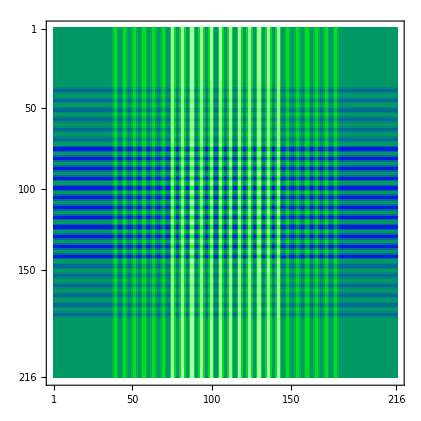

```mathematica
MatrixPlot[alicesScores,Evaluate@commonOpts]
```

```mathematica
ascoreSpecific
```

Cos[z2/2]^2 (3 Cos[z1/2]^2+((3 Cos[x1]^2)/2+5 Sin[x1]^2 (Cos[y1]^2/2+Sin[y1]^2)) Sin[z1/2]^2)+Sin[x1]^2 (5 Cos[x2]^2+Cos[y2]^2 Sin[x2]^2) (Cos[y1]^2+Sin[y1]^2/2) Sin[z1/2]^2 Sin[z2/2]^2+1/4 (4 (Sin[x1]^2 Sin[x2]^2 (Cos[y1]^2/2+Sin[y1]^2) Sin[y2]^2 Sin[z1/2]^2+3 Cos[x2]^2 (1/2 Cos[z1/2]^2+Cos[x1]^2 Sin[z1/2]^2))+(4 (-6 Cos[x1] Cos[x2] Cos[y2] Sin[x1] Sin[x2] Sin[y1]+Cos[y1] Sin[2 x1] Sin[2 x2] Sin[y2]) Sin[z1/2]^2+8 Cos[y1] Cos[y2] Sin[x1] Sin[2 x2] Sin[z1])/(√2)) Sin[z2/2]^2-1/4 Cos[x2] (5 Sin[x1]^2 Sin[2 y1] Sin[z1/2]^2+3 Cos[x1] Sin[z1]) Sin[z2]+1/4 (2 (Cos[x1]^2 Cos[z2/2]^2 Sin[z1/2]^2+Cos[x2]^2 Cos[z1/2]^2 Sin[z2/2]^2+Sin[x2]^2 Sin[y2] (3 Cos[y1]^2 Sin[x1]^2 Sin[y2] Sin[z1/2]^2+5 Cos[x1] Cos[y2] Sin[z1]) Sin[z2/2]^2)+Cos[x1] Cos[x2] Sin[z1] Sin[z2])+1/(4 √2)Sin[x2] (2 √2 Sin[x2] (Sin[y2] (6 Cos[y1] Cos[y2] Sin[x1]^2 Sin[y1]+5 Cos[x1]^2 Sin[y2]) Sin[z1/2]^2+Cos[y2]^2 (5 Cos[z1/2]^2+3 Sin[x1]^2 Sin[y1]^2 Sin[z1/2]^2)) Sin[z2/2]^2-(8 Sin[2 x1] Sin[y1] Sin[y2] Sin[z1/2]^2+2 Sin[x1] (2 Cos[y2] Sin[y1]-3 Cos[y1] Sin[y2]) Sin[z1]) Sin[z2])+(Sin[x1] Sin[x2] (Cos[x2] Sin[y1] Sin[y2] Sin[z1] Sin[z2/2]^2-Cos[y1] Cos[y2] Sin[z1/2]^2 (√2 Sin[x1] Sin[x2] Sin[y1] Sin[y2] Sin[z2/2]^2+Cos[x1] Sin[z2])))/(√2)

```mathematica
ascore
```

Cos[z2/2]^2 (3 Cos[z1/2]^2+(3 Cos[x1]^2 Cos[γ]^2 Cos[b γ]^2+5 Sin[x1]^2 (Cos[y1]^2 Cos[γ]^2 Cos[b γ]^2+Sin[y1]^2)) Sin[z1/2]^2)+Cos[a γ]^2 Sin[x1]^2 (5 Cos[x2]^2+Cos[y2]^2 Sin[x2]^2) (Cos[y1]^2 Cos[b γ]^2+Cos[γ]^2 Sin[y1]^2) Sin[z1/2]^2 Sin[z2/2]^2-1/2 Cos[x2] Cos[a γ] Cos[b γ] (5 Sin[x1]^2 Sin[2 y1] Sin[z1/2]^2+3 Cos[x1] Sin[z1]) Sin[z2] Sin[γ]^2+1/2 (2 (Cos[x1]^2 Cos[z2/2]^2 Cos[(b γ)/2]^4 Sin[z1/2]^2+Cos[x2]^2 Cos[z1/2]^2 Cos[(a γ)/2]^4 Sin[z2/2]^2+Cos[b γ] Sin[x2]^2 Sin[y2] (3 Cos[y1]^2 Cos[b γ] Sin[x1]^2 Sin[y2] Sin[z1/2]^2+5 Cos[x1] Cos[y2] Cos[a γ] Sin[z1]) Sin[z2/2]^2)+Cos[x1] Cos[x2] Cos[(a γ)/2]^2 Cos[(b γ)/2]^2 Sin[z1] Sin[z2]) Sin[γ]^2+1/4 Sin[z2/2]^2 (4 (Sin[x1]^2 Sin[x2]^2 (Cos[y1]^2 Cos[γ]^2 Cos[b γ]^2+Sin[y1]^2) Sin[y2]^2 Sin[z1/2]^2+3 Cos[x2]^2 Cos[a γ]^2 (Cos[z1/2]^2 Cos[γ]^2+Cos[x1]^2 Cos[b γ]^2 Sin[z1/2]^2))+Cos[a γ] Cos[b γ] (4 (-6 Cos[x1] Cos[x2] Cos[y2] Cos[a γ] Sin[x1] Sin[x2] Sin[y1]+Cos[y1] Cos[b γ] Sin[2 x1] Sin[2 x2] Sin[y2]) Sin[z1/2]^2+Cos[y1] Cos[y2] (-1+9 Cos[a γ]) Sin[x1] Sin[2 x2] Sin[z1]) Sin[γ])+1/4 Sin[x2] Sin[γ] (-(((-1+9 Cos[b γ]) Sin[2 x1] Sin[y1] Sin[y2] Sin[z1/2]^2+2 Sin[x1] (2 Cos[y2] Cos[a γ] Sin[y1]-3 Cos[y1] Cos[b γ] Sin[y2]) Sin[z1]) Sin[z2])+4 Sin[x2] (Cos[b γ] Sin[y2] (6 Cos[y1] Cos[y2] Cos[a γ] Sin[x1]^2 Sin[y1]+5 Cos[x1]^2 Cos[b γ] Sin[y2]) Sin[z1/2]^2+Cos[y2]^2 Cos[a γ]^2 (5 Cos[z1/2]^2+3 Sin[x1]^2 Sin[y1]^2 Sin[z1/2]^2)) Sin[z2/2]^2 Sin[γ])+Sin[x1] Sin[x2] Sin[γ] (Cos[x2] Cos[(a γ)/2]^2 Sin[y1] Sin[y2] Sin[z1] Sin[z2/2]^2-Cos[y1] Cos[y2] Cos[a γ] Cos[b γ] Sin[z1/2]^2 (Cos[x1] Cos[(b γ)/2]^2 Sin[z2]+2 Sin[x1] Sin[x2] Sin[y1] Sin[y2] Sin[z2/2]^2 Sin[γ]))+Cos[x2] Sin[x1] Sin[x2] (Cos[y1] Cos[y2] Cos[a γ] Cos[b γ]-Sin[y1] Sin[y2]) Sin[z1] Sin[z2/2]^2 Sin[γ] Sin[(a γ)/2]^2+1/2 Cos[y2] Cos[b γ] Sin[x2] (-5 Cos[γ]^2 Sin[x1]^2 Sin[2 y1] Sin[z1/2]^2+3 Cos[x1] Sin[z1]) Sin[z2] Sin[a γ]-1/2 Sin[x2] (2 Cos[x2] (2 Cos[y2] Cos[z1/2]^2 Cos[(a γ)/2]^2-Cos[b γ] Sin[y2] (3 Sin[x1]^2 Sin[2 y1] Sin[z1/2]^2+5 Cos[x1] Sin[z1])) Sin[z2/2]^2+Cos[x1] Cos[y2] Cos[(b γ)/2]^2 Sin[z1] Sin[z2]) Sin[γ]^2 Sin[a γ]+1/2 (Cos[b γ] Sin[x2] (4 Cos[x2] Cos[y1] Cos[γ]^2 Sin[x1]^2 Sin[y1] Sin[y2] Sin[z1/2]^2 Sin[z2/2]^2+Cos[y2] (5 Sin[x1]^2 Sin[2 y1] Sin[z1/2]^2-3 Cos[x1] Cos[γ]^2 Sin[z1]) Sin[z2])+2 Sin[x1] (-Cos[y2] Sin[x2]^2 Sin[y2] (4 Cos[x1] Cos[y1] Cos[b γ]^2 Sin[z1/2]^2+Sin[y1] Sin[z1]) Sin[z2/2]^2-Cos[x2] (Cos[x1] Cos[y1] Cos[(b γ)/2]^2 Cos[b γ] Sin[z1/2]^2+Sin[y1] Sin[z1]) Sin[z2]) Sin[γ]) Sin[a γ]+(Cos[y2]^2 Cos[b γ]^2 (3 Cos[x1]^2+5 Cos[y1]^2 Sin[x1]^2) Sin[x2]^2+Cos[x2]^2 Sin[x1]^2 (Cos[y1]^2 Cos[b γ]^2+Cos[γ/2]^4 Sin[y1]^2)) Sin[z1/2]^2 Sin[z2/2]^2 Sin[a γ]^2+1/2 Sin[z2/2]^2 Sin[a γ] (2 Sin[x1] (Sin[x1] Sin[y1]^2 Sin[z1/2]^2 (5 Cos[y2]^2 Cos[γ]^2 Sin[x2]^2+Cos[x2]^2 Sin[γ/2]^4)+2 Cos[x2] Cos[y2] Cos[b γ] Sin[x2] (3 Cos[x1] Sin[y1] Sin[z1/2]^2-2 Cos[y1] Sin[z1]) Sin[γ]) Sin[a γ]+Cos[z1/2]^2 (4 Cos[x2] Cos[y2] Sin[x2] Sin[γ]^2 Sin[(a γ)/2]^2+2 Cos[y2]^2 (2+Cos[2 γ]) Sin[x2]^2 Sin[a γ]+9 Cos[x2]^2 Sin[γ]^2 Sin[a γ]))+1/2 (Cos[x2] Sin[z1] Sin[γ] Sin[(a γ)/2]^2 (-Cos[x1] Cos[(b γ)/2]^2 Sin[z2] Sin[γ]+2 Cos[x2] Cos[y1] Cos[b γ] Sin[x1] Sin[z2/2]^2 Sin[a γ])-Cos[y2] Cos[b γ]^2 (3 Cos[x1]^2+4 Cos[y1]^2 Sin[x1]^2) Sin[2 x2] Sin[z1/2]^2 Sin[z2/2]^2 Sin[2 a γ]+Sin[z2/2]^2 (-Sin[y1] Sin[z1/2]^2 (Cos[y2] Cos[γ] Sin[x1]^2 Sin[2 x2] Sin[y1] Sin[γ/2]^2+3 Cos[x2]^2 Cos[b γ] Sin[2 x1] Sin[γ])+Cos[y2] Sin[γ] (-4 Cos[y1] Cos[y2] Cos[b γ] Sin[x1] Sin[x2]^2 Sin[z1]+5 Cos[z1/2]^2 Sin[2 x2] Sin[γ])) Sin[2 a γ])+1/4 Sin[z2/2]^2 (-8 Cos[x2] Cos[y1] Cos[b γ] Sin[x1]^2 Sin[x2] Sin[y1] Sin[y2] Sin[z1/2]^2 Sin[a γ]+Cos[y2] Sin[y1] Sin[z1/2]^2 (Cos[γ] Sin[x1]^2 Sin[2 x2] Sin[y1]-9 Cos[γ]^2 Sin[x1]^2 Sin[2 x2] Sin[y1]+6 Cos[y2] Cos[b γ] Sin[2 x1] Sin[x2]^2 Sin[γ]) Sin[2 a γ]+Cos[x2]^2 Sin[γ] (4 Cos[z1/2]^2 Sin[γ] Sin[(a γ)/2]^4+Cos[y1] Cos[b γ] Sin[x1] Sin[z1] (-2 Sin[a γ]+9 Sin[2 a γ])))+1/2 (Sin[z2/2]^2 (5 Cos[x2]^2 Sin[x1]^2 Sin[y1]^2 Sin[z1/2]^2 Sin[γ]^2 Sin[a γ]^2-3 Cos[y2] Cos[z1/2]^2 Cos[γ]^2 Sin[2 x2] Sin[2 a γ])-Cos[x1] Sin[z2] Sin[γ] (2 Sin[x1] Sin[x2] Sin[y1] Sin[y2] Sin[z1/2]^2+Cos[x2] Cos[(a γ)/2]^2 Sin[z1] Sin[γ]) Sin[(b γ)/2]^2-Cos[x1] Sin[z2] Sin[γ] Sin[(b γ)/2] (4 Cos[x1] Cos[x2] Cos[(b γ)/2]^3 Sin[z1/2]^2 Sin[a γ]-(Cos[x2] Sin[z1] Sin[γ] Sin[(a γ)/2]^2+2 Cos[y1] Cos[b γ] Sin[x1] Sin[z1/2]^2 (Cos[y2] Cos[a γ] Sin[x2]+Cos[x2] Sin[a γ])) Sin[(b γ)/2]))-1/2 Sin[x1] (Cos[y1] Sin[z1] (Cos[x2] Cos[(a γ)/2]^2 Sin[z2]+Cos[a γ] (5 Sin[x2]^2 Sin[2 y2] Sin[z2/2]^2-3 Cos[x2] Sin[z2]))+2 Cos[x1] Sin[z1/2]^2 (2 Cos[y1] Cos[z2/2]^2 Cos[(b γ)/2]^2+Cos[a γ] Sin[y1] (-3 Sin[x2]^2 Sin[2 y2] Sin[z2/2]^2+5 Cos[x2] Sin[z2]))) Sin[γ]^2 Sin[b γ]+Sin[x2] Sin[γ] (Cos[y2] Cos[a γ] (Cos[y1]^2 Cos[b γ] Sin[x1]^2 Sin[z1/2]^2 Sin[z2]+Cos[x1] Sin[z2/2]^2 (5 Cos[x2] Cos[a γ] Sin[z1]-2 Sin[x1] Sin[x2] Sin[y1] Sin[y2] Sin[z1/2]^2 Sin[γ]))+Sin[x1] (-5 Cos[x2] Cos[y1] Sin[y2] Sin[z1] Sin[z2/2]^2+Cos[x1] Sin[y1] Sin[z1/2]^2 (6 Cos[x2] Sin[y2] Sin[z2/2]^2+5 Cos[y2] Sin[z2])) Sin[γ] Sin[a γ]) Sin[b γ]-1/2 (Cos[y1] Sin[x1] Sin[z2] Sin[γ] (-2 Cos[x2] Cos[y1] Cos[b γ] Sin[x1] Sin[z1/2]^2+3 Cos[y2] Sin[x2] Sin[z1] Sin[γ]) Sin[a γ]+2 Cos[x1] Cos[x2] Sin[z2/2]^2 (2 Cos[x2] Cos[(a γ)/2]^3 Sin[z1] Sin[γ] Sin[(a γ)/2]+Sin[x2] (-Cos[y2] Cos[a γ] Sin[z1] Sin[γ] Sin[(a γ)/2]^2+4 (1+Cos[γ]) Sin[x1] Sin[y1] Sin[y2] Sin[z1/2]^2 Sin[γ/2]^2 Sin[a γ]))) Sin[b γ]+1/2 Sin[γ] (Cos[x2] Sin[z1] (Cos[y1] Sin[x1] Sin[z2] Sin[γ] Sin[(a γ)/2]^2-8 Cos[x1] Cos[y2] Sin[x2] Sin[z2/2]^2 Sin[a γ]^2)+Cos[x2]^2 Sin[z2/2]^2 (Cos[x1] (1+9 Cos[a γ]) Sin[z1] Sin[a γ]+3 Sin[x1]^2 Sin[2 y1] Sin[z1/2]^2 Sin[2 a γ])+Cos[y2] Sin[x1] (Cos[y1] Sin[x2] Sin[z1] Sin[z2] Sin[γ] Sin[a γ]-3 Sin[x1] Sin[2 y1] Sin[z1/2]^2 Sin[z2/2]^2 (Sin[2 x2] Sin[a γ]^2+Cos[y2] Sin[x2]^2 Sin[2 a γ]))) Sin[b γ]+1/2 Sin[z1/2]^2 (2 (Cos[x2]^2 Cos[a γ]^2 (5 Cos[x1]^2+3 Cos[y1]^2 Sin[x1]^2)+Cos[x1]^2 Sin[x2]^2 (Cos[y2]^2 Cos[a γ]^2+Cos[γ]^2 Sin[y2]^2)) Sin[z2/2]^2+Sin[γ] (2 Cos[x1] Cos[y1] Cos[a γ] Sin[x1] Sin[x2] (-4 Cos[x2] Sin[y2] Sin[z2/2]^2+Cos[y2] Sin[z2])-Cos[z2/2]^2 (Cos[x1]^2-2 Cos[y1]^2 Sin[x1]^2) Sin[γ])) Sin[b γ]^2+Sin[z1/2]^2 (Cos[x1] Cos[x2] Cos[y1] Sin[x1] Sin[z2] Sin[γ] Sin[a γ]+Cos[y1] Sin[x2]^2 Sin[z2/2]^2 (Sin[2 x1] Sin[2 y2] Sin[γ] Sin[a γ]+Cos[y1] Sin[x1]^2 (5 Sin[y2]^2 Sin[γ]^2+3 Cos[y2]^2 Sin[a γ]^2))+Cos[x1]^2 Sin[z2/2]^2 (Cos[x2]^2 Sin[a γ]^2+Sin[x2]^2 (3 Sin[y2]^2 Sin[γ]^2+5 Cos[y2]^2 Sin[a γ]^2)-2 Cos[y2] Sin[2 x2] Sin[2 a γ])) Sin[b γ]^2+Sin[b γ] (2 Cos[x1] Sin[γ] (-Cos[y2]^2 Sin[x2]^2 Sin[z1] Sin[z2/2]^2 Sin[2 a γ]+Cos[y1] Cos[z2/2]^2 Sin[x1] Sin[z1/2]^2 Sin[γ] Sin[(b γ)/2]^2)+Cos[z2/2]^2 Cos[γ]^2 (5 Cos[x1]^2+3 Cos[y1]^2 Sin[x1]^2) Sin[z1/2]^2 Sin[b γ])+1/2 Sin[γ] (Sin[z1/2]^2 (Cos[y2] (3 Sin[x1]^2 Sin[2 x2] Sin[y1]^2 Sin[z2/2]^2 Sin[γ] Sin[2 a γ]-4 Cos[x1]^2 Cos[a γ] Cos[(b γ)/2]^3 Sin[x2] Sin[z2] Sin[(b γ)/2])+2 Cos[x1]^2 Sin[(b γ)/2]^3 (2 Cos[x2] Cos[(b γ)/2] Sin[z2] Sin[a γ]+Cos[z2/2]^2 Sin[γ] Sin[(b γ)/2]))+Sin[x2] (2 Cos[x2] Cos[y2] Cos[a γ] (6 Cos[y1] Cos[a γ] Sin[x1]^2 Sin[y1] Sin[z1/2]^2-Cos[x1] Cos[(a γ)/2]^2 Sin[z1]) Sin[z2/2]^2+Sin[y2] (8 Cos[y1] Sin[x1]^2 Sin[y1] Sin[z1/2]^2+3 Cos[x1] Sin[z1]) Sin[z2]) Sin[b γ])+1/4 Sin[y2] Sin[z1/2]^2 Sin[z2/2]^2 (Cos[y1] (-1+3 Cos[2 γ]) Sin[2 x1] Sin[x2]^2 Sin[y2]+4 Cos[x1]^2 Cos[a γ] Sin[2 x2] Sin[γ]-4 Cos[y1]^2 Cos[a γ] Sin[x1]^2 Sin[2 x2] Sin[γ]) Sin[2 b γ]+1/2 (Cos[x1] Cos[y2] Sin[x2] Sin[z2] Sin[γ] Sin[(b γ)/2]^2 (Sin[z1] Sin[γ] Sin[a γ]+2 Cos[x1] Cos[a γ] Sin[z1/2]^2 Sin[b γ])+Cos[y1] Cos[a γ]^2 Sin[2 x1] (2 Cos[x2]^2+Cos[y2]^2 Sin[x2]^2) Sin[z1/2]^2 Sin[z2/2]^2 Sin[2 b γ]+Sin[z1/2]^2 Sin[z2/2]^2 Sin[a γ] (-2 (Cos[x1]^2-Cos[y1]^2 Sin[x1]^2) Sin[x2]^2 Sin[2 y2] Sin[γ]+Cos[y1] Sin[2 x1] (Cos[x2]^2+2 Cos[y2]^2 Sin[x2]^2) Sin[a γ]) Sin[2 b γ])-1/2 Cos[y1] Sin[z1/2]^2 (6 Cos[y1] Cos[y2] Sin[x1]^2 Sin[2 x2] Sin[z2/2]^2 Sin[2 a γ] Sin[b γ]^2+Sin[2 x1] (-4 Cos[z2/2]^2 Cos[γ]^2+Cos[y2] Sin[2 x2] Sin[z2/2]^2 Sin[2 a γ]) Sin[2 b γ])

```mathematica
(*2. Convert to a Python-style string*)
pyString=ToString[ascore,FortranForm];
(* ->"(sin(x)**2 + cos(y)**2)/(exp(z) + log(x*y))"*)

(*3. Replace the bare function names with numpy calls*)
needs={"Sin"->"np.sin","Cos"->"np.cos","Exp"->"np.exp","Log"->"np.log","γ"->"g"};
pyStringWithNP=StringReplace[pyString,needs]
(*
->"(np.sin(x)**2 + np.cos(y)**2)/(np.exp(z) + np.log(x*y))"*)

(*4. Wrap it in a little module header and write to disk*)
moduleText=StringJoin["import numpy as np\n\n","def f(x, y, z):\n","    return ",pyStringWithNP,"\n"];
Export["myfunc.py",moduleText,"Text"]
```

np.cos(z2/2.)**2*(3*np.cos(z1/2.)**2 + (3*np.cos(x1)**2*np.cos(g)**2*np.cos(b*g)**2 + 5*np.sin(x1)**2*(np.cos(y1)**2*np.cos(g)**2*np.cos(b*g)**2 + np.sin(y1)**2))*np.sin(z1/2.)**2) + np.cos(a*g)**2*np.sin(x1)**2*(5*np.cos(x2)**2 + np.cos(y2)**2*np.sin(x2)**2)*(np.cos(y1)**2*np.cos(b*g)**2 + np.cos(g)**2*np.sin(y1)**2)*np.sin(z1/2.)**2*np.sin(z2/2.)**2 - (np.cos(x2)*np.cos(a*g)*np.cos(b*g)*(5*np.sin(x1)**2*np.sin(2*y1)*np.sin(z1/2.)**2 + 3*np.cos(x1)*np.sin(z1))*np.sin(z2)*np.sin(g)**2)/2. + ((2*(np.cos(x1)**2*np.cos(z2/2.)**2*np.cos((b*g)/2.)**4*np.sin(z1/2.)**2 + np.cos(x2)**2*np.cos(z1/2.)**2*np.cos((a*g)/2.)**4*np.sin(z2/2.)**2 + np.cos(b*g)*np.sin(x2)**2*np.sin(y2)*(3*np.cos(y1)**2*np.cos(b*g)*np.sin(x1)**2*np.sin(y2)*np.sin(z1/2.)**2 + 5*np.cos(x1)*np.cos(y2)*np.cos(a*g)*np.sin(z1))*np.sin(z2/2.)**2) + np.cos(x1)*np.cos(x2)*np.cos((a*g)/2.)**2*np.cos((b*g)/2.)**2*np.sin(z1)*np.sin(z2))*np.sin(g)**2)/2. + (np.sin(z2/2.)**2*(4*(np.sin(x1)**2*np.sin(x2)**2*(np.cos(y1)**2*np.cos(g)**2*np.cos(b*g)**2 + np.sin(y1)**2)*np.sin(y2)**2*np.sin(z1/2.)**2 + 3*np.cos(x2)**2*np.cos(a*g)**2*(np.cos(z1/2.)**2*np.cos(g)**2 + np.cos(x1)**2*np.cos(b*g)**2*np.sin(z1/2.)**2)) + np.cos(a*g)*np.cos(b*g)*(4*(-6*np.cos(x1)*np.cos(x2)*np.cos(y2)*np.cos(a*g)*np.sin(x1)*np.sin(x2)*np.sin(y1) + np.cos(y1)*np.cos(b*g)*np.sin(2*x1)*np.sin(2*x2)*np.sin(y2))*np.sin(z1/2.)**2 + np.cos(y1)*np.cos(y2)*(-1 + 9*np.cos(a*g))*np.sin(x1)*np.sin(2*x2)*np.sin(z1))*np.sin(g)))/4. + (np.sin(x2)*np.sin(g)*(-(((-1 + 9*np.cos(b*g))*np.sin(2*x1)*np.sin(y1)*np.sin(y2)*np.sin(z1/2.)**2 + 2*np.sin(x1)*(2*np.cos(y2)*np.cos(a*g)*np.sin(y1) - 3*np.cos(y1)*np.cos(b*g)*np.sin(y2))*np.sin(z1))*np.sin(z2)) + 4*np.sin(x2)*(np.cos(b*g)*np.sin(y2)*(6*np.cos(y1)*np.cos(y2)*np.cos(a*g)*np.sin(x1)**2*np.sin(y1) + 5*np.cos(x1)**2*np.cos(b*g)*np.sin(y2))*np.sin(z1/2.)**2 + np.cos(y2)**2*np.cos(a*g)**2*(5*np.cos(z1/2.)**2 + 3*np.sin(x1)**2*np.sin(y1)**2*np.sin(z1/2.)**2))*np.sin(z2/2.)**2*np.sin(g)))/4. + np.sin(x1)*np.sin(x2)*np.sin(g)*(np.cos(x2)*np.cos((a*g)/2.)**2*np.sin(y1)*np.sin(y2)*np.sin(z1)*np.sin(z2/2.)**2 - np.cos(y1)*np.cos(y2)*np.cos(a*g)*np.cos(b*g)*np.sin(z1/2.)**2*(np.cos(x1)*np.cos((b*g)/2.)**2*np.sin(z2) + 2*np.sin(x1)*np.sin(x2)*np.sin(y1)*np.sin(y2)*np.sin(z2/2.)**2*np.sin(g))) + np.cos(x2)*np.sin(x1)*np.sin(x2)*(np.cos(y1)*np.cos(y2)*np.cos(a*g)*np.cos(b*g) - np.sin(y1)*np.sin(y2))*np.sin(z1)*np.sin(z2/2.)**2*np.sin(g)*np.sin((a*g)/2.)**2 + (np.cos(y2)*np.cos(b*g)*np.sin(x2)*(-5*np.cos(g)**2*np.sin(x1)**2*np.sin(2*y1)*np.sin(z1/2.)**2 + 3*np.cos(x1)*np.sin(z1))*np.sin(z2)*np.sin(a*g))/2. - (np.sin(x2)*(2*np.cos(x2)*(2*np.cos(y2)*np.cos(z1/2.)**2*np.cos((a*g)/2.)**2 - np.cos(b*g)*np.sin(y2)*(3*np.sin(x1)**2*np.sin(2*y1)*np.sin(z1/2.)**2 + 5*np.cos(x1)*np.sin(z1)))*np.sin(z2/2.)**2 + np.cos(x1)*np.cos(y2)*np.cos((b*g)/2.)**2*np.sin(z1)*np.sin(z2))*np.sin(g)**2*np.sin(a*g))/2. + ((np.cos(b*g)*np.sin(x2)*(4*np.cos(x2)*np.cos(y1)*np.cos(g)**2*np.sin(x1)**2*np.sin(y1)*np.sin(y2)*np.sin(z1/2.)**2*np.sin(z2/2.)**2 + np.cos(y2)*(5*np.sin(x1)**2*np.sin(2*y1)*np.sin(z1/2.)**2 - 3*np.cos(x1)*np.cos(g)**2*np.sin(z1))*np.sin(z2)) + 2*np.sin(x1)*(-(np.cos(y2)*np.sin(x2)**2*np.sin(y2)*(4*np.cos(x1)*np.cos(y1)*np.cos(b*g)**2*np.sin(z1/2.)**2 + np.sin(y1)*np.sin(z1))*np.sin(z2/2.)**2) - np.cos(x2)*(np.cos(x1)*np.cos(y1)*np.cos((b*g)/2.)**2*np.cos(b*g)*np.sin(z1/2.)**2 + np.sin(y1)*np.sin(z1))*np.sin(z2))*np.sin(g))*np.sin(a*g))/2. + (np.cos(y2)**2*np.cos(b*g)**2*(3*np.cos(x1)**2 + 5*np.cos(y1)**2*np.sin(x1)**2)*np.sin(x2)**2 + np.cos(x2)**2*np.sin(x1)**2*(np.cos(y1)**2*np.cos(b*g)**2 + np.cos(g/2.)**4*np.sin(y1)**2))*np.sin(z1/2.)**2*np.sin(z2/2.)**2*np.sin(a*g)**2 + (np.sin(z2/2.)**2*np.sin(a*g)*(2*np.sin(x1)*(np.sin(x1)*np.sin(y1)**2*np.sin(z1/2.)**2*(5*np.cos(y2)**2*np.cos(g)**2*np.sin(x2)**2 + np.cos(x2)**2*np.sin(g/2.)**4) + 2*np.cos(x2)*np.cos(y2)*np.cos(b*g)*np.sin(x2)*(3*np.cos(x1)*np.sin(y1)*np.sin(z1/2.)**2 - 2*np.cos(y1)*np.sin(z1))*np.sin(g))*np.sin(a*g) + np.cos(z1/2.)**2*(4*np.cos(x2)*np.cos(y2)*np.sin(x2)*np.sin(g)**2*np.sin((a*g)/2.)**2 + 2*np.cos(y2)**2*(2 + np.cos(2*g))*np.sin(x2)**2*np.sin(a*g) + 9*np.cos(x2)**2*np.sin(g)**2*np.sin(a*g))))/2. + (np.cos(x2)*np.sin(z1)*np.sin(g)*np.sin((a*g)/2.)**2*(-(np.cos(x1)*np.cos((b*g)/2.)**2*np.sin(z2)*np.sin(g)) + 2*np.cos(x2)*np.cos(y1)*np.cos(b*g)*np.sin(x1)*np.sin(z2/2.)**2*np.sin(a*g)) - np.cos(y2)*np.cos(b*g)**2*(3*np.cos(x1)**2 + 4*np.cos(y1)**2*np.sin(x1)**2)*np.sin(2*x2)*np.sin(z1/2.)**2*np.sin(z2/2.)**2*np.sin(2*a*g) + np.sin(z2/2.)**2*(-(np.sin(y1)*np.sin(z1/2.)**2*(np.cos(y2)*np.cos(g)*np.sin(x1)**2*np.sin(2*x2)*np.sin(y1)*np.sin(g/2.)**2 + 3*np.cos(x2)**2*np.cos(b*g)*np.sin(2*x1)*np.sin(g))) + np.cos(y2)*np.sin(g)*(-4*np.cos(y1)*np.cos(y2)*np.cos(b*g)*np.sin(x1)*np.sin(x2)**2*np.sin(z1) + 5*np.cos(z1/2.)**2*np.sin(2*x2)*np.sin(g)))*np.sin(2*a*g))/2. + (np.sin(z2/2.)**2*(-8*np.cos(x2)*np.cos(y1)*np.cos(b*g)*np.sin(x1)**2*np.sin(x2)*np.sin(y1)*np.sin(y2)*np.sin(z1/2.)**2*np.sin(a*g) + np.cos(y2)*np.sin(y1)*np.sin(z1/2.)**2*(np.cos(g)*np.sin(x1)**2*np.sin(2*x2)*np.sin(y1) - 9*np.cos(g)**2*np.sin(x1)**2*np.sin(2*x2)*np.sin(y1) + 6*np.cos(y2)*np.cos(b*g)*np.sin(2*x1)*np.sin(x2)**2*np.sin(g))*np.sin(2*a*g) + np.cos(x2)**2*np.sin(g)*(4*np.cos(z1/2.)**2*np.sin(g)*np.sin((a*g)/2.)**4 + np.cos(y1)*np.cos(b*g)*np.sin(x1)*np.sin(z1)*(-2*np.sin(a*g) + 9*np.sin(2*a*g)))))/4. + (np.sin(z2/2.)**2*(5*np.cos(x2)**2*np.sin(x1)**2*np.sin(y1)**2*np.sin(z1/2.)**2*np.sin(g)**2*np.sin(a*g)**2 - 3*np.cos(y2)*np.cos(z1/2.)**2*np.cos(g)**2*np.sin(2*x2)*np.sin(2*a*g)) - np.cos(x1)*np.sin(z2)*np.sin(g)*(2*np.sin(x1)*np.sin(x2)*np.sin(y1)*np.sin(y2)*np.sin(z1/2.)**2 + np.cos(x2)*np.cos((a*g)/2.)**2*np.sin(z1)*np.sin(g))*np.sin((b*g)/2.)**2 - np.cos(x1)*np.sin(z2)*np.sin(g)*np.sin((b*g)/2.)*(4*np.cos(x1)*np.cos(x2)*np.cos((b*g)/2.)**3*np.sin(z1/2.)**2*np.sin(a*g) - (np.cos(x2)*np.sin(z1)*np.sin(g)*np.sin((a*g)/2.)**2 + 2*np.cos(y1)*np.cos(b*g)*np.sin(x1)*np.sin(z1/2.)**2*(np.cos(y2)*np.cos(a*g)*np.sin(x2) + np.cos(x2)*np.sin(a*g)))*np.sin((b*g)/2.)))/2. - (np.sin(x1)*(np.cos(y1)*np.sin(z1)*(np.cos(x2)*np.cos((a*g)/2.)**2*np.sin(z2) + np.cos(a*g)*(5*np.sin(x2)**2*np.sin(2*y2)*np.sin(z2/2.)**2 - 3*np.cos(x2)*np.sin(z2))) + 2*np.cos(x1)*np.sin(z1/2.)**2*(2*np.cos(y1)*np.cos(z2/2.)**2*np.cos((b*g)/2.)**2 + np.cos(a*g)*np.sin(y1)*(-3*np.sin(x2)**2*np.sin(2*y2)*np.sin(z2/2.)**2 + 5*np.cos(x2)*np.sin(z2))))*np.sin(g)**2*np.sin(b*g))/2. + np.sin(x2)*np.sin(g)*(np.cos(y2)*np.cos(a*g)*(np.cos(y1)**2*np.cos(b*g)*np.sin(x1)**2*np.sin(z1/2.)**2*np.sin(z2) + np.cos(x1)*np.sin(z2/2.)**2*(5*np.cos(x2)*np.cos(a*g)*np.sin(z1) - 2*np.sin(x1)*np.sin(x2)*np.sin(y1)*np.sin(y2)*np.sin(z1/2.)**2*np.sin(g))) + np.sin(x1)*(-5*np.cos(x2)*np.cos(y1)*np.sin(y2)*np.sin(z1)*np.sin(z2/2.)**2 + np.cos(x1)*np.sin(y1)*np.sin(z1/2.)**2*(6*np.cos(x2)*np.sin(y2)*np.sin(z2/2.)**2 + 5*np.cos(y2)*np.sin(z2)))*np.sin(g)*np.sin(a*g))*np.sin(b*g) - ((np.cos(y1)*np.sin(x1)*np.sin(z2)*np.sin(g)*(-2*np.cos(x2)*np.cos(y1)*np.cos(b*g)*np.sin(x1)*np.sin(z1/2.)**2 + 3*np.cos(y2)*np.sin(x2)*np.sin(z1)*np.sin(g))*np.sin(a*g) + 2*np.cos(x1)*np.cos(x2)*np.sin(z2/2.)**2*(2*np.cos(x2)*np.cos((a*g)/2.)**3*np.sin(z1)*np.sin(g)*np.sin((a*g)/2.) + np.sin(x2)*(-(np.cos(y2)*np.cos(a*g)*np.sin(z1)*np.sin(g)*np.sin((a*g)/2.)**2) + 4*(1 + np.cos(g))*np.sin(x1)*np.sin(y1)*np.sin(y2)*np.sin(z1/2.)**2*np.sin(g/2.)**2*np.sin(a*g))))*np.sin(b*g))/2. + (np.sin(g)*(np.cos(x2)*np.sin(z1)*(np.cos(y1)*np.sin(x1)*np.sin(z2)*np.sin(g)*np.sin((a*g)/2.)**2 - 8*np.cos(x1)*np.cos(y2)*np.sin(x2)*np.sin(z2/2.)**2*np.sin(a*g)**2) + np.cos(x2)**2*np.sin(z2/2.)**2*(np.cos(x1)*(1 + 9*np.cos(a*g))*np.sin(z1)*np.sin(a*g) + 3*np.sin(x1)**2*np.sin(2*y1)*np.sin(z1/2.)**2*np.sin(2*a*g)) + np.cos(y2)*np.sin(x1)*(np.cos(y1)*np.sin(x2)*np.sin(z1)*np.sin(z2)*np.sin(g)*np.sin(a*g) - 3*np.sin(x1)*np.sin(2*y1)*np.sin(z1/2.)**2*np.sin(z2/2.)**2*(np.sin(2*x2)*np.sin(a*g)**2 + np.cos(y2)*np.sin(x2)**2*np.sin(2*a*g))))*np.sin(b*g))/2. + (np.sin(z1/2.)**2*(2*(np.cos(x2)**2*np.cos(a*g)**2*(5*np.cos(x1)**2 + 3*np.cos(y1)**2*np.sin(x1)**2) + np.cos(x1)**2*np.sin(x2)**2*(np.cos(y2)**2*np.cos(a*g)**2 + np.cos(g)**2*np.sin(y2)**2))*np.sin(z2/2.)**2 + np.sin(g)*(2*np.cos(x1)*np.cos(y1)*np.cos(a*g)*np.sin(x1)*np.sin(x2)*(-4*np.cos(x2)*np.sin(y2)*np.sin(z2/2.)**2 + np.cos(y2)*np.sin(z2)) - np.cos(z2/2.)**2*(np.cos(x1)**2 - 2*np.cos(y1)**2*np.sin(x1)**2)*np.sin(g)))*np.sin(b*g)**2)/2. + np.sin(z1/2.)**2*(np.cos(x1)*np.cos(x2)*np.cos(y1)*np.sin(x1)*np.sin(z2)*np.sin(g)*np.sin(a*g) + np.cos(y1)*np.sin(x2)**2*np.sin(z2/2.)**2*(np.sin(2*x1)*np.sin(2*y2)*np.sin(g)*np.sin(a*g) + np.cos(y1)*np.sin(x1)**2*(5*np.sin(y2)**2*np.sin(g)**2 + 3*np.cos(y2)**2*np.sin(a*g)**2)) + np.cos(x1)**2*np.sin(z2/2.)**2*(np.cos(x2)**2*np.sin(a*g)**2 + np.sin(x2)**2*(3*np.sin(y2)**2*np.sin(g)**2 + 5*np.cos(y2)**2*np.sin(a*g)**2) - 2*np.cos(y2)*np.sin(2*x2)*np.sin(2*a*g)))*np.sin(b*g)**2 + np.sin(b*g)*(2*np.cos(x1)*np.sin(g)*(-(np.cos(y2)**2*np.sin(x2)**2*np.sin(z1)*np.sin(z2/2.)**2*np.sin(2*a*g)) + np.cos(y1)*np.cos(z2/2.)**2*np.sin(x1)*np.sin(z1/2.)**2*np.sin(g)*np.sin((b*g)/2.)**2) + np.cos(z2/2.)**2*np.cos(g)**2*(5*np.cos(x1)**2 + 3*np.cos(y1)**2*np.sin(x1)**2)*np.sin(z1/2.)**2*np.sin(b*g)) + (np.sin(g)*(np.sin(z1/2.)**2*(np.cos(y2)*(3*np.sin(x1)**2*np.sin(2*x2)*np.sin(y1)**2*np.sin(z2/2.)**2*np.sin(g)*np.sin(2*a*g) - 4*np.cos(x1)**2*np.cos(a*g)*np.cos((b*g)/2.)**3*np.sin(x2)*np.sin(z2)*np.sin((b*g)/2.)) + 2*np.cos(x1)**2*np.sin((b*g)/2.)**3*(2*np.cos(x2)*np.cos((b*g)/2.)*np.sin(z2)*np.sin(a*g) + np.cos(z2/2.)**2*np.sin(g)*np.sin((b*g)/2.))) + np.sin(x2)*(2*np.cos(x2)*np.cos(y2)*np.cos(a*g)*(6*np.cos(y1)*np.cos(a*g)*np.sin(x1)**2*np.sin(y1)*np.sin(z1/2.)**2 - np.cos(x1)*np.cos((a*g)/2.)**2*np.sin(z1))*np.sin(z2/2.)**2 + np.sin(y2)*(8*np.cos(y1)*np.sin(x1)**2*np.sin(y1)*np.sin(z1/2.)**2 + 3*np.cos(x1)*np.sin(z1))*np.sin(z2))*np.sin(b*g)))/2. + (np.sin(y2)*np.sin(z1/2.)**2*np.sin(z2/2.)**2*(np.cos(y1)*(-1 + 3*np.cos(2*g))*np.sin(2*x1)*np.sin(x2)**2*np.sin(y2) + 4*np.cos(x1)**2*np.cos(a*g)*np.sin(2*x2)*np.sin(g) - 4*np.cos(y1)**2*np.cos(a*g)*np.sin(x1)**2*np.sin(2*x2)*np.sin(g))*np.sin(2*b*g))/4. + (np.cos(x1)*np.cos(y2)*np.sin(x2)*np.sin(z2)*np.sin(g)*np.sin((b*g)/2.)**2*(np.sin(z1)*np.sin(g)*np.sin(a*g) + 2*np.cos(x1)*np.cos(a*g)*np.sin(z1/2.)**2*np.sin(b*g)) + np.cos(y1)*np.cos(a*g)**2*np.sin(2*x1)*(2*np.cos(x2)**2 + np.cos(y2)**2*np.sin(x2)**2)*np.sin(z1/2.)**2*np.sin(z2/2.)**2*np.sin(2*b*g) + np.sin(z1/2.)**2*np.sin(z2/2.)**2*np.sin(a*g)*(-2*(np.cos(x1)**2 - np.cos(y1)**2*np.sin(x1)**2)*np.sin(x2)**2*np.sin(2*y2)*np.sin(g) + np.cos(y1)*np.sin(2*x1)*(np.cos(x2)**2 + 2*np.cos(y2)**2*np.sin(x2)**2)*np.sin(a*g))*np.sin(2*b*g))/2. - (np.cos(y1)*np.sin(z1/2.)**2*(6*np.cos(y1)*np.cos(y2)*np.sin(x1)**2*np.sin(2*x2)*np.sin(z2/2.)**2*np.sin(2*a*g)*np.sin(b*g)**2 + np.sin(2*x1)*(-4*np.cos(z2/2.)**2*np.cos(g)**2 + np.cos(y2)*np.sin(2*x2)*np.sin(z2/2.)**2*np.sin(2*a*g))*np.sin(2*b*g)))/2.

myfunc.py